## cGA

uczenie się na podstawie najlepszego i najgorszego osobnika wg wzoru
p_i=Piecewise[{{p_i+1/N, x_i=1 i y_i=0}, {p_i-1/N, x_i=0 i y_i=1}, {p_i, pozostale}}]    ,  x- najlepszy osobnik, y-najgorszy

```mathematica
Clear[cGA,valuate,compareW,compareB];
```

```mathematica
(*funkcja zliczająca jedynki*)
valuate[x_]:=Module[{val=0, n= Length[x],i=0,j=0,k=0},
For[i=1,i<=n,i++,val+=x⟦i⟧];
val];
(*n-dł osobnika, f-funkcja optymalizowana, size-rozmiar populacji, max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm*)
cGA[n_,f_,size_,max_,itmax_]:=Module[{P=Table[0.5,{n}],best,worst,population=Table[Table[0,{n}],{size}], iter=0,wynik=Table[{0,0},{1}]},
(*generacja pop startowej*)
SeedRandom[];
(*Porównywanie wartości funkcji dla osobników B-zwraca wiekszy, W-mniejszy*)
compareB[x_,y_]:=If[f[x]>f[y],x,y];
compareW[x_,y_]:=If[f[x]<f[y],x,y];
For[j=1,j≤size,j++,
For[i=1,i≤n,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{1,0}]
]];
(*ustalenie najlepszego osobnika z populacji*)
best=population⟦1⟧;
worst=best;
(*Print[population];*)
(*Print["best:",best];*)

(*Algorytm kończy działanie po osiągnięciu max albo ilości iteracji*)
While[(f[best]≠max  && iter≠itmax ),
(*wyszukiwanie najlepszego osobnika*)
For[i=1,i≤size,i++,best=compareB[population⟦i⟧,best]];
(*wyszukiwanie najgorszego*)
For[i=1,i≤size,i++,worst=compareW[population⟦i⟧,worst]];
(*Print["best:",best," iter: ",iter];*)
wynik⟦iter⟧={iter,f[best]};
(*Obliczenie nowego wektora prawdopodobienstwa*)
For[i=1,i≤n,i++,
If[best⟦i⟧==1&&worst⟦i⟧==0,P⟦i⟧+=1/size,
If[best⟦i⟧==0 && worst⟦i⟧==1,P⟦i⟧-=1/size]]];
(*Gdy prawdopodobienstwo ujemne -> zamiana na 0, gdy większe od 1 na 1*)
For[i=1,i≤n,i++,If[P⟦i⟧<0,(*Print[P[[i]]];*)P⟦i⟧=0(*;Print[P[[i]]]*),P⟦i⟧=Mod[P⟦i⟧,1]]];
(*Generacja nowej populacji*)
For[j=1,j≤size,j++,
For[i=1,i≤n,i++,(*Print["P[",i,"]=",P⟦i⟧,"1-P[",i,"]=",1-P⟦i⟧];*)
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
]];

iter++;
wynik2=Table[{iter,f[best]},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];

Print["Wartosc ",f[best],"(",max,") uzyskane po iteracjach: ",iter];
Print[best];
(*Print[wynik];*)
ListLinePlot[wynik]
]
```

Testy

#### trap

```mathematica
trap[k_,x_]:= If[valuate[x]<k,k-1-valuate[x],k]
```

trap_k(u)=Piecewise[{{k-1 - u,, u<k}, {k,, inaczej}}]
trap_5(u)=Piecewise[{{4- u,, u<5}, {k,, inaczej}}]

trap5

Wartosc 5(5) uzyskane po iteracjach: 1

{1,1,1,1,1}

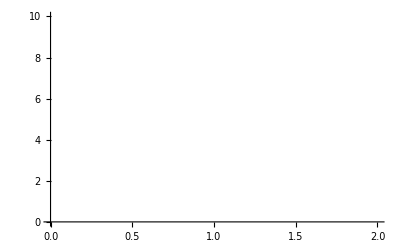

```mathematica
trap5[x_]:=trap[5,x];
cGA[5,trap5,20,5,100]
```

trap5

Maximum (5) uzyskane po iteracjach: 1

{1,1,1,1,1}

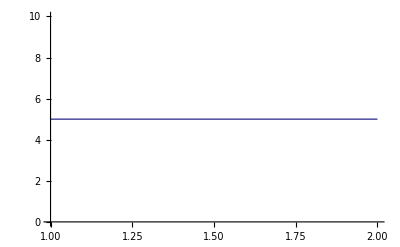

```mathematica
cGA[5,trap5,20,5,100]
```

trap6 6-bit, 20 osobnikow

```mathematica
trap6[x_]:=trap[6,x];
```

Maximum (6) uzyskane po iteracjach: 1

{1,1,1,1,1,1}

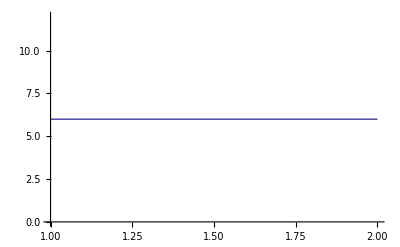

```mathematica
cGA[6,trap6,20,6,100]
```

trap6 6bit populacja 20os

Maximum (6) uzyskane po iteracjach: 4

{1,1,1,1,1,1}

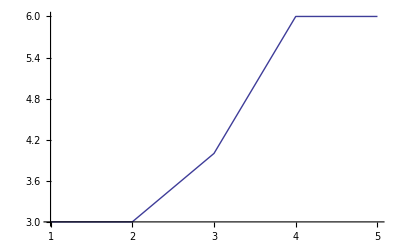

```mathematica
cGA[6,trap6,20,6,100]
```

trap6 populacja 5os

Maximum (6) uzyskane po iteracjach: 3

{1,1,1,1,1,1}

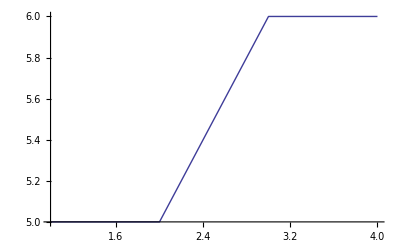

```mathematica
cGA[6,trap6,5,6,100]
```

trap6

```mathematica
cGA[6,trap6,20,6,100]
```

Wartosc 6(6) uzyskane po iteracjach: 3

{1,1,1,1,1,1}

-Graphics-

### valuate dla 10 bit, 20 osobnikow, max 100iteracji

Wartosc 10(10) uzyskane po iteracjach: 11

{1,1,1,1,1,1,1,1,1,1}

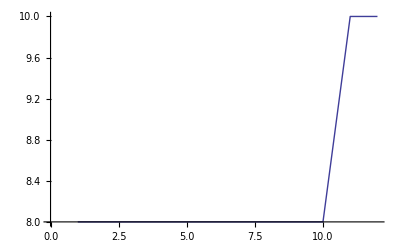

```mathematica
cGA[10,valuate,20,10,100]
```

### 3deceptive

f_(3deceptive)(u)=Piecewise[{{0.9, u=0}, {0.8, u=1}, {0, u=2}, {1, inaczej}}]

```mathematica
f3d[x_]:=Module[{q=valuate[x]},
If[q==0,0.9,
If[q==1,0.8,
If[q==2,0,1]]]];
```

```mathematica
f3d[{0,0,0,0,1}]
```

0.8

3 deceptive dl=5, 20 osobnikow

Wartosc 1(1) uzyskane po iteracjach: 1

{1,1,1,0,1}

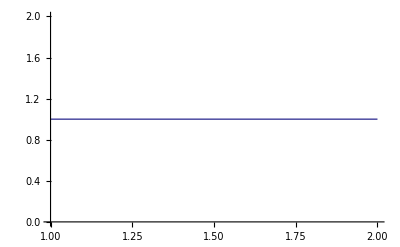

```mathematica
cGA[5,f3d,20,1,100]
```

3 deceptive, 3-bit 5-osobnikow

Wartosc 1(1) uzyskane po iteracjach: 4

{1,1,1}

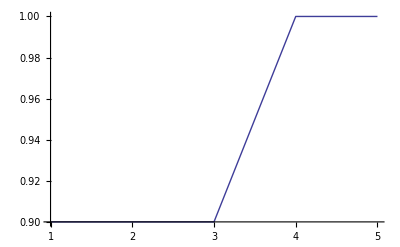

```mathematica
cGA[3,f3d,5,1,100]
```

```mathematica
3 deceptive, 3-bit,
cGA[3,f3d,5,1,100]
```

3 deceptive, 3-bit, 20 osobnikow

```mathematica
cGA[3,f3d,20,1,100]
```

Wartosc 1(1) uzyskane po iteracjach: 1

{1,1,1}

-Graphics-

3 deceptive 4-bit 20 os

Wartosc 1(1) uzyskane po iteracjach: 0

{0,1,1,1}

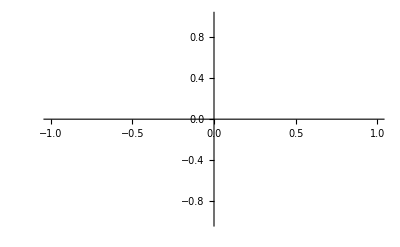

```mathematica
cGA[4,f3d,20,1,100]
```

3 deceptive 4-bit 5 osobnikow

```mathematica
cGA[4,f3d,5,1,100]
```

Wartosc 1(1) uzyskane po iteracjach: 1

{0,1,1,1}

-Graphics-

3 deceptive 4-bit populacja 5

```mathematica
cGA[4,f3d,5,1,100]
```

Wartosc 1(1) uzyskane po iteracjach: 1

{1,1,1,0}

-Graphics-

TESTY 100 EL

```mathematica
(*funkcja zliczająca jedynki*)
valuate[x_]:=Module[{val=0, n= Length[x],i=0,j=0,k=0},
For[i=1,i<=n,i++,val+=x⟦i⟧];
val];
(*n-dł osobnika, f-funkcja optymalizowana, size-rozmiar populacji, max-rzeczywiste maximum funkcji, itmax - ilość iteracji, która kończy algorytm*)
cGAtest[n_,f_,size_,max_,itmax_]:=Module[{P=Table[0.5,{n}],best,worst,population=Table[Table[0,{n}],{size}], iter=0,wynik=Table[{0,0},{1}]},
(*generacja pop startowej*)
SeedRandom[];
(*Porównywanie wartości funkcji dla osobników B-zwraca wiekszy, W-mniejszy*)
compareB[x_,y_]:=If[f[x]>f[y],x,y];
compareW[x_,y_]:=If[f[x]<f[y],x,y];
For[j=1,j≤size,j++,
For[i=1,i≤n,i++,
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{1,0}]
]];
(*ustalenie najlepszego osobnika z populacji*)
best=population⟦1⟧;
worst=best;
(*Print[population];*)
(*Print["best:",best];*)

(*Algorytm kończy działanie po osiągnięciu max albo ilości iteracji*)
While[(f[best]≠max  && iter≠itmax ),
(*wyszukiwanie najlepszego osobnika*)
For[i=1,i≤size,i++,best=compareB[population⟦i⟧,best]];
(*wyszukiwanie najgorszego*)
For[i=1,i≤size,i++,worst=compareW[population⟦i⟧,worst]];
(*Print["best:",best," iter: ",iter];*)
wynik⟦iter⟧={iter,f[best]};
(*Obliczenie nowego wektora prawdopodobienstwa*)
For[i=1,i≤n,i++,
If[best⟦i⟧==1&&worst⟦i⟧==0,P⟦i⟧+=1/size,
If[best⟦i⟧==0 && worst⟦i⟧==1,P⟦i⟧-=1/size]]];
(*Gdy prawdopodobienstwo ujemne -> zamiana na 0, gdy większe od 1 na 1*)
For[i=1,i≤n,i++,If[P⟦i⟧<0,(*Print[P[[i]]];*)P⟦i⟧=0(*;Print[P[[i]]]*),P⟦i⟧=Mod[P⟦i⟧,1]]];
(*Generacja nowej populacji*)
For[j=1,j≤size,j++,
For[i=1,i≤n,i++,(*Print["P[",i,"]=",P⟦i⟧,"1-P[",i,"]=",1-P⟦i⟧];*)
population⟦j,i⟧=RandomChoice[{P⟦i⟧,1-P⟦i⟧}->{0,1}]
]];

iter++;
wynik2=Table[{iter,f[best]},{iter}];
For[i=1,i<iter,i++,wynik2⟦i⟧=wynik⟦i⟧];
wynik=wynik2;
];

(*Print["Wartosc ",f[best],"(",max,") uzyskane po iteracjach: ",iter];
Print[best];
(*Print[wynik];*)
ListLinePlot[wynik]*)
Return[{iter,Abs[max-f[best]]}]
]
```

#### trap

```mathematica
trap[k_,x_]:= If[valuate[x]<k,k-1-valuate[x],k]
```

trap_k(u)=Piecewise[{{k-1 - u,, u<k}, {k,, inaczej}}]
trap_5(u)=Piecewise[{{4- u,, u<5}, {k,, inaczej}}]

trap5

```mathematica
trap5[x_]:=trap[5,x];

size = {5,20,50};max=5;n=5;iter=100;
For[jj=1,jj<=Length[size],jj++,
wyn=0; it=0;
For[q=1,q<=100,q++,
wyn=cGAtest[n,trap5,size⟦jj⟧,max,iter];
it+=wyn];
Print["size = ",size⟦jj⟧," it = ",it/100.];
];
```

size = 5 it = 2.84

size = 20 it = 1.87

size = 50 it = 1.15

trap6 6-bit

```mathematica
trap6[x_]:=trap[6,x];
```

```mathematica
size = {5,20,50,100};max=6;n=6;iter=100;
For[jj=1,jj<=Length[size],jj++,
wyn=0; it=0;
For[q=1,q<=100,q++,
wyn=cGAtest[n,trap6,size⟦jj⟧,max,iter];
it+=wyn];
Print["size = ",size⟦jj⟧," it = ",it/100.];
];
```

size = 5 it = 3.55

size = 20 it = 2.65

size = 50 it = 1.71

size = 100 it = 1.24

trap7 7-bit

```mathematica
trap7[x_]:=trap[7,x];
```

```mathematica
size = {5,20,50,100,200};max=7;n=7;iter=100;
For[jj=1,jj<=Length[size],jj++,
wyn=0; it=0;
For[q=1,q<=100,q++,
wyn=cGAtest[n,trap7,size⟦jj⟧,max,iter];
it+=wyn];
Print["size = ",size⟦jj⟧," it = ",it/100.];
];
```

size = 5 it = 4.24

size = 20 it = 3.46

size = 50 it = 2.6

size = 100 it = 1.86

size = 200 it = 1.22

trap7 7-bit

```mathematica
trap7[x_]:=trap[7,x];
```

```mathematica
size = {5,20,50,100,200};max=7;n=7;iter=100;
For[jj=1,jj<=Length[size],jj++,
wyn=0; it=0;
For[q=1,q<=100,q++,
wyn=cGAtest[n,trap7,size⟦jj⟧,max,iter];
it+=wyn];
Print["size = ",size⟦jj⟧," it = ",it/100.];
];
```

trap10 10-bit

```mathematica
trap10[x_]:=trap[10,x];
```

```mathematica
Clear[trap10,jj,wyn,bl]
```

```mathematica
size = {5,20,50,100,200,500};max=10;n=10;iter=100;
For[jj=1,jj<=Length[size],jj++,
wyn={0,0}; it=0;bl=0;
For[q=1,q<=100,q++,
wyn=cGAtest[n,trap10,size⟦jj⟧,max,iter];
it+=wyn⟦1⟧;
bl+=wyn⟦2⟧
];
Print["size = ",size⟦jj⟧," it = ",it/100., " bł: ",bl/100.];
];
```

size = 5 it = 6.75 bł: 0.

size = 20 it = 6.37 bł: 0.

size = 50 it = 6.44 bł: 0.

size = 100 it = 6.38 bł: 0.

$Aborted

### 3deceptive

f_(3deceptive)(u)=Piecewise[{{0.9, u=0}, {0.8, u=1}, {0, u=2}, {1, inaczej}}]

```mathematica
f3d[x_]:=Module[{q=valuate[x]},
If[q==0,0.9,
If[q==1,0.8,
If[q==2,0,1]]]];
```

```mathematica
f3d[{0,0,0,0,1}]
```

0.8

3 deceptive dl=5, 20 osobnikow

```mathematica
size = {5,20,50,100,200,500};max=1;n={3,5,10};iter=100;
For[qj=1,qj≤Length[n],qj++,
Print["__________________"];
Print["n = ",n[[qj]]];
For[jj=1,jj<=Length[size],jj++,
wyn={0,0}; it=0;bl=0;
For[q=1,q<=100,q++,
wyn=cGAtest[n[[qj]],f3d,size⟦jj⟧,max,iter];
it+=wyn[[1]];
bl+=wyn[[2]]];
Print["size = ",size⟦jj⟧," it = ",it/100.," bl: ",bl/100.];
]];
```

__________________

n = 3

size = 5 it = 1.8 bl: 0.

size = 20 it = 0.92 bl: 0.

size = 50 it = 0.87 bl: 0.

size = 100 it = 0.89 bl: 0.

size = 200 it = 0.87 bl: 0.

size = 500 it = 0.82 bl: 0.

__________________

n = 5

size = 5 it = 0.41 bl: 0.

size = 20 it = 0.51 bl: 0.

size = 50 it = 0.53 bl: 0.

size = 100 it = 0.5 bl: 0.

size = 200 it = 0.48 bl: 0.

size = 500 it = 0.52 bl: 0.

__________________

n = 10

size = 5 it = 0.11 bl: 0.

size = 20 it = 0.06 bl: 0.

size = 50 it = 0.06 bl: 0.

size = 100 it = 0.13 bl: 0.

size = 200 it = 0.05 bl: 0.

size = 500 it = 0.04 bl: 0.